```mathematica
ClearAll["Global`*"]
```

```mathematica
ode1=m x''[t]+c x'[t]+k x[t]==F0 Cos[ω t+ϕd]
ode2=x''[t]+2 β x'[t]+ω0^2 x[t]==A0 Cos[ω t+ϕd]
```

k x[t]+c x'[t]+m x''[t]==F0 Cos[ϕd+t ω]

ω0^2 x[t]+2 β x'[t]+x''[t]==A0 Cos[ϕd+t ω]

{{x→InterpolatingFunction[…]}}

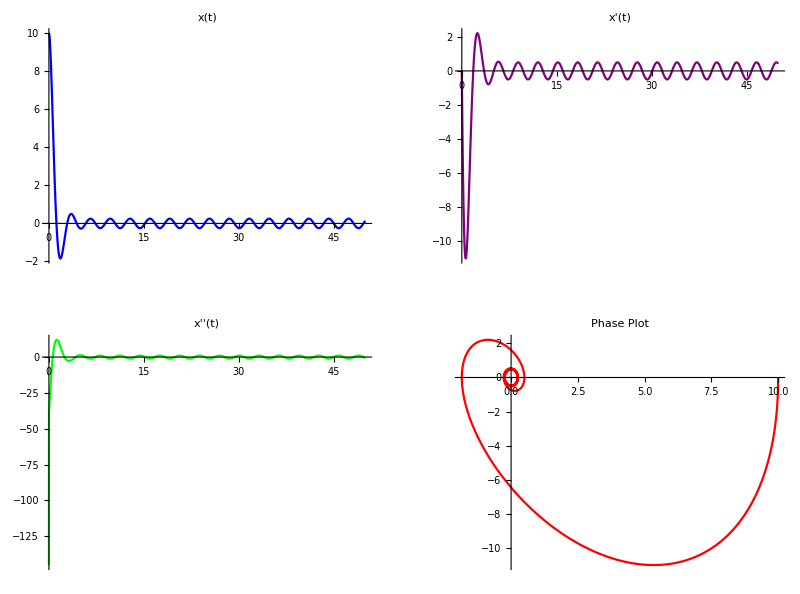

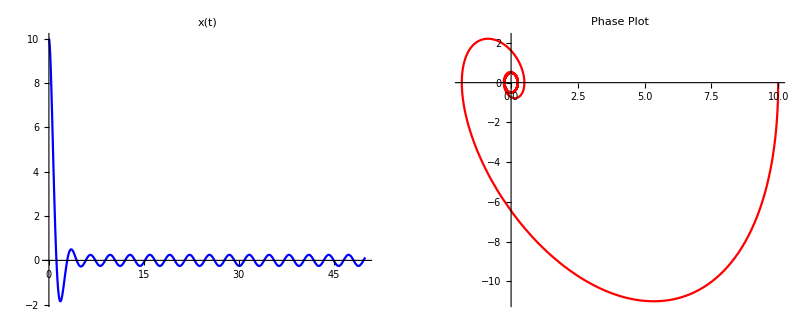

```mathematica
T:=50
x0:=10
dx0:=0

β:=1
ω0:=2
A0:=1
ω:=2.001
ϕd:=Pi/3

m:=1
c:=0.1
k:=1
F0:=1

soln2=NDSolve[{ode2,x[0]==x0,x'[0]==dx0},x,{t,0,T}]

xplot:=Plot[Evaluate[x[t]/.soln2],{t,0,T},PlotRange->All,PlotLabel->"x(t)",PlotStyle->{Blue}]
dxplot:=Plot[Evaluate[x'[t]/.soln2],{t,0,T},PlotRange->All,PlotLabel->"x'(t)",PlotStyle->{Purple}]
ddxplot:=Plot[Evaluate[x''[t]/.soln2],{t,0,T},PlotRange->All,PlotLabel->"x''(t)",PlotStyle->{Green}]
phaseplot:=ParametricPlot[Evaluate[{x[t],x'[t]}/.soln2],{t,0,T},PlotRange->All,PlotLabel->"Phase Plot",PlotStyle->{Red}]

GraphicsGrid[{{xplot,dxplot},{ddxplot,phaseplot}},Frame->All,ImageSize->Automatic]
GraphicsRow[{xplot,phaseplot},Frame->All]
```